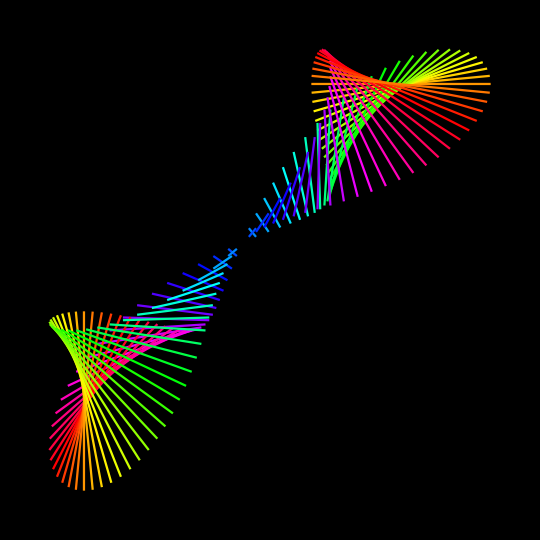
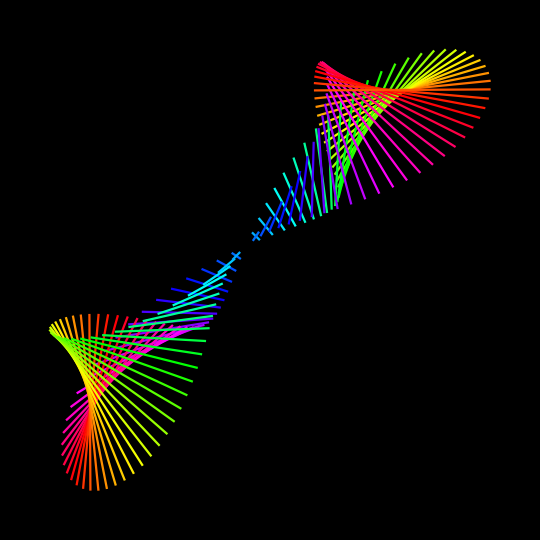
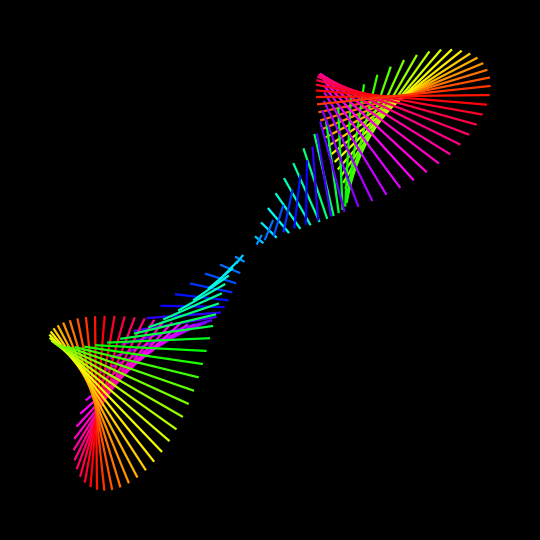
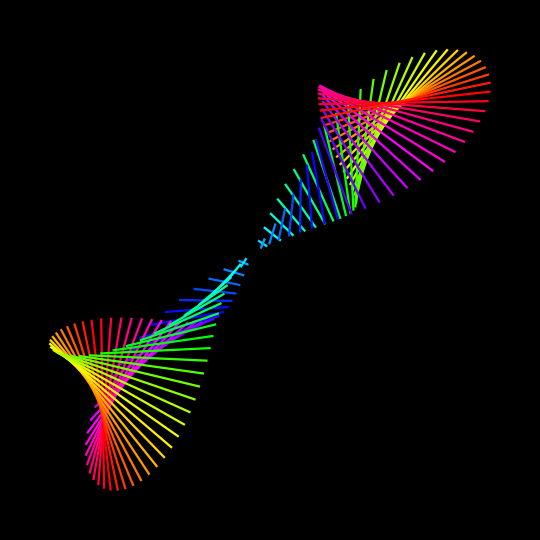
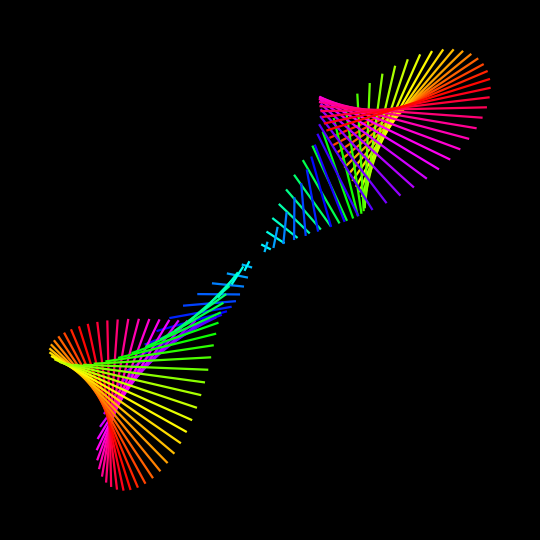
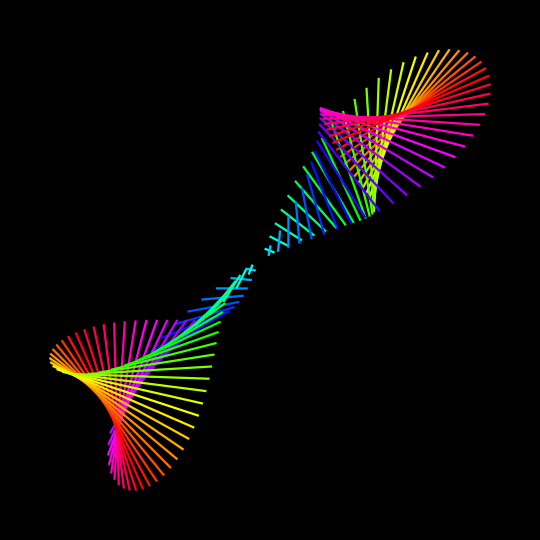
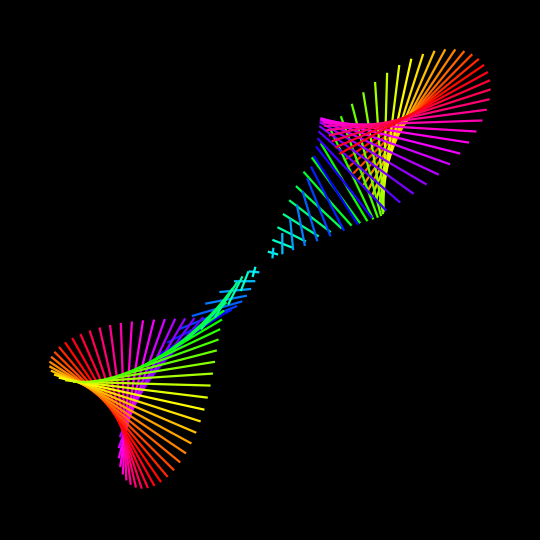
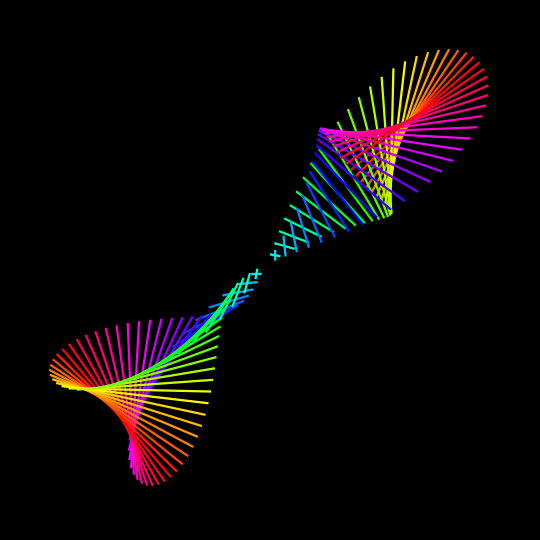

```mathematica
animationorient=With[{n=100},   Table[Graphics[{CapForm["Round"],Thickness[.003],Table[{Hue[Mod[2θ+t^2, 4π]/(2 π)],Line[{#,#}+RotationTransform[3/2 θ+t][.4 {-#,#}]]&[{Cos[θ],Cos[θ]}]},{θ,0,2 π-2 π/n,2 π/n}]},
                  PlotRange->2,ImageSize->540,Background->Black,
                  Epilog->{Text[Style["@nathanaelnoir",12,White,FontFamily->"Helvetica"],{1.5,-1.8}]}
],
{t,-π/4,2 π-π/4,0.1}]
]
Export["anim.gif",animationorient,ImageResolution->300]
```